## PHAS2443 2014 exam Hayk Khachatryan

## Question 1

```mathematica
Select[Range[2,2000], PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999}

## Question 2

```mathematica
ψ = z/r

rV = {x,y,z}

p= -ⅈ ℏ ∇_{x,y,z} # &

L = rV × p[#] &

L[ψ]
```

z/r

{x,y,z}

-ⅈ ℏ #1{x,y,z}&

rV×p[#1]&

{-(ⅈ y ℏ)/r,(ⅈ x ℏ)/r,0}

```mathematica
ϕ = L[ψ][[1]] + ⅈ L[ψ][[2]]
```

-(x ℏ)/r-(ⅈ y ℏ)/r

```mathematica
Simplify[(L[ϕ][[3]])/ϕ]
```

ℏ

## Question 3

```mathematica
Clear[ψ]
schro = {-1/2 D[ψ[x,t], {x, 2}] + V[x]ψ[x,t] == ⅈ D[ψ[x,t], t]}

V[x_] := 10 ⅇ^(-x^2)

bc = {ψ[-10, t] == ⅇ^(ⅈ (π x)/5)ⅇ^(-(x+5)^2) /. x-> -10, ψ[5,t] == ⅇ^(ⅈ (π x)/5)ⅇ^(-(x+5)^2) /. x-> 5}
```

{10 ⅇ^(-x^2) ψ[x,t]-1/2 ψ^(2,0)[x,t]==ⅈ ψ^(0,1)[x,t]}

{ψ[-10,t]==1/ⅇ^25,ψ[5,t]==-1/ⅇ^100}

```mathematica
sol = NDSolve[
Join[schro, bc],
ψ[x,t],
{x, -10, 5},
{t, 0, 2.5}]
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

{{ψ[x,t]→InterpolatingFunction[{{-10., 5.}, {0., 2.5}}, <>][x,t]}}

```mathematica
Exp[ⅈ π x/5] Exp[−(x+5)^2] //. x-> 5
```

-1/ⅇ^100

```mathematica
Plot3D[
Re[ψ[x,t] /. sol],
{x, -10, 5},
{t, 0, 2.5},
AxesLabel->{"x", "t", "amp"},
ViewPoint -> {0, -Infinity, Infinity}]
```

-Graphics3D-

```mathematica
Clear[eq, ψ, V]

eq = {-1/2 D[ψ[x,t], {x, 2}] + V[x]ψ[x,t] == ⅈ D[ψ[x,t], t]}
V[x_] := 10 ⅇ^(-x^2)
bc = {ψ[x,0] == ⅇ^(ⅈ π x/5)ⅇ^(-(x+5)^2),ψ[-10, t] == 1/ⅇ^25, ψ[5,t] == -1/ⅇ^100}
```

{V[x] ψ[x,t]-1/2 ψ^(2,0)[x,t]==ⅈ ψ^(0,1)[x,t]}

{ψ[x,0]==ⅇ^((ⅈ π x)/5-(5+x)^2),ψ[-10,t]==1/ⅇ^25,ψ[5,t]==-1/ⅇ^100}

```mathematica
sol = NDSolve[
Join[eq, bc],
ψ[x,t],
{x, -10, 5},
{t, 0, 2.5}

]
```

{{ψ[x,t]→InterpolatingFunction[{{-10., 5.}, {0., 2.5}}, <>][x,t]}}

```mathematica
Plot3D[
Re[ψ[x,t] /. sol],
{x, -10, 5},
{t, 0, 2.5},
Mesh->None,
ColorFunction->"SouthwestColors",
ViewPoint->{0, -2, 0}]
```

-Graphics3D-

```mathematica
Clear[eq, ψ, V]

eq = {-0.5D[ψ[x,t], {x,2}]+V[x]ψ[x,t] == ⅈ D[ψ[x,t], t]}
```

## Question 4

```mathematica
p =Plot3D[
LaguerreL[3, √(x^2+y^2)],
{x, -3, 3},
{y, -3,3},Mesh -> None, ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
pp = ParametricPlot3D[{Cos[u], Sin[u], 0}, {u, 0, 2π}]
```

-Graphics3D-

```mathematica
Show[p, pp]
```

-Graphics3D-

## Question 5

{x[t]+6 x'[t]+x''[t]==1/2 Sin[3 t]}

{x[0]==3,x'[0]==0}

{{x→InterpolatingFunction[{{0., 30.}}, <>]}}

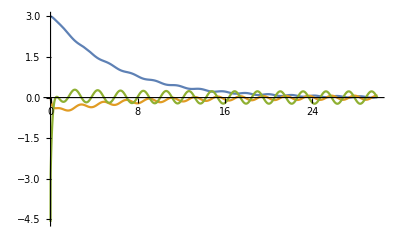

```mathematica
Clear[eq,bc, sol] 

eq = {x''[t] + 6x'[t] + x[t] == 1/2 Sin[3t]}
bc ={x[0] == 3, x'[0] == 0}

sol = 
NDSolve[
Join[eq, bc],
x,
{t, 0, 30}]

Plot[{x[t] /. sol,x'[t] /. sol, x''[t] /. sol}, {t, 0, 30}, PlotRange->All]
```

## Question 6

```mathematica
Clear[c]
c[f_,n_] := (2n+1)/2 Integrate[f[x] LegendreP[n,x], {x, -1,1}]
```

```mathematica
Clear[f]
f= Cos[#] + 3 ⅇ^(-#^2) &
```

Cos[#1]+3 ⅇ^(-#1^2)&

```mathematica
Clear[functioner]
functioner[f_, n_,x_] := 
Sum[
c[f,i] LegendreP[i,x],
{i, 0, n}]
```

```mathematica
f5 = functioner[f, 5,x]
```

5/4 (-1+3 x^2) (-9/(2 ⅇ)+6 Cos[1]+3/4 √π Erf[1]-4 Sin[1])+1/2 (3 √π Erf[1]+2 Sin[1])+9/16 (3-30 x^2+35 x^4) (-345/(16 ⅇ)-190 Cos[1]+171/32 √π Erf[1]+122 Sin[1])

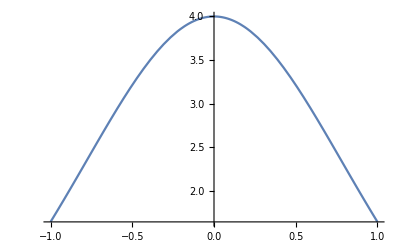

```mathematica
Plot[f[x], {x, -1,1}]
```

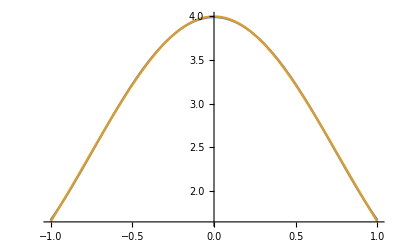

```mathematica
Plot[{f5, f[x]}, {x, -1,1}]
```

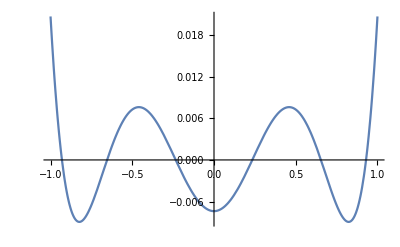

```mathematica
Plot[f5 - f[x], {x, -1,1}]
```

## Question 7

```mathematica
Δt = 0.1

B  = {0,0,1}

T = B Δt/2
S = 2 T/(1+Norm[T]^2)
```

0.1

{0,0,1}

{0.,0.,0.05}

{0.,0.,0.0997506}

```mathematica
function[{x_,v_}] :=
Module[
{xP,vP,xPP,vPP},
xP = x + Δt/2 v;
vP = v + (v×T);

vPP = v + (vP×S);
xPP = xP + Δt/2 vPP;

{xPP, vPP}]
```

```mathematica
s = NestList[function,{{0,1,0}, {10,0,0.5}}, 1000]
```

{{{0,1,0},{10,0,0.5}},{{0.997506,0.950125,0.05},{9.95012,-0.997506,0.5}},997,{{-6.5493,-1.44311,49.95},{7.55689,6.5493,0.5}},{{-5.76283,-0.8275,50.},{8.1725,5.76283,0.5}}}
 |  |  |  |

```mathematica
xes = Transpose[s][[1]];

ListPointPlot3D[xes, AxesLabel->{"x", "y", "z"}, ViewPoint->{1.3, -2.4, 2.}] /. Point -> Line
```

-Graphics3D-

```mathematica
ves = Transpose[s][[2]];
kes  = Norm[#]^2 & /@ ves;

Mean[kes]
StandardDeviation[kes]
```

100.25

9.56613×10^-14

## Question 8

```mathematica
u1 = Table[RandomReal[], 10000]
u2= Table[RandomReal[], 10000]
```

{0.683841,0.0699244,0.565391,0.082021,0.613939,0.744991,0.0495064,0.424218,0.3725,0.0836181,9980,0.141295,0.145608,0.543996,0.211544,0.0716258,0.198586,0.0489069,0.680158,0.710949,0.220361}
 |  |  |  |

{0.41452,0.143419,0.171823,0.95457,0.734041,0.902365,0.303009,0.822678,0.281829,0.796356,9980,0.524575,0.610899,0.0201668,0.738207,0.365092,0.577735,0.479843,0.433697,0.425677,0.245705}
 |  |  |  |

```mathematica
z0 = 3(√(-2 Log[u1]) Cos[2π u2]) + 1

Mean[z0]
StandardDeviation[z0]


z1 = 3(√(-2 Log[u1]) Sin[2π u2]) + 1

Mean[z1]
StandardDeviation[z1]
```

{-1.24719,5.29542,2.51118,7.43777,0.703345,2.88221,-1.40478,2.73235,0.162434,2.91919,9980,-4.86439,-3.51647,4.28385,0.608537,-3.55852,-3.76349,-6.31125,-1.40869,-1.21273,1.1408}
 |  |  |  |

1.01817

2.99043

{2.33816,6.42545,3.825,-0.889228,-1.94847,-0.325216,7.95117,-2.5262,5.13205,-5.40185,1.20538,9979,0.0872085,-2.77949,1.41834,-4.2732,6.16462,-1.53116,1.93095,2.06582,2.11562,6.21584}
 |  |  |  |

0.984498

2.97014

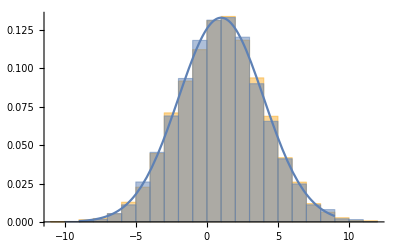

```mathematica
p = Plot[PDF[NormalDistribution[1,3],x], {x, -9,9}];
h = Histogram[{z0,z1}, Automatic, "PDF"];

Show[h,p]
```

```mathematica
Max[Re[Sqrt[(-2 Log[S])] v1/(√S)]]
```

```mathematica
0.;
```

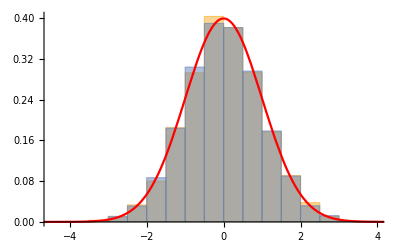

```mathematica
v1 = Table[RandomReal[{-1,1}], 10000];
v2 = Table[RandomReal[{-1,1}], 10000];

S = Flatten[v1^2 + v2^2];

w0 = Select[Flatten[Sqrt[(-2 Log[S])] v1/(√S)], Head[#] == Real &];
w1 = Select[Flatten[Sqrt[(-2Log[S])] v2/(√S)], Head[#] == Real &];


p = Plot[PDF[NormalDistribution[0,1],x], {x, -5,5}, PlotStyle->Red];
h = Histogram[{w0,w1}, Automatic, "PDF"];
Show[h,p]
```

## Question 9

```mathematica
eq = {D[u[t,x], t] == D[u[t,x], x,x]}
bc = {u[0,x] == 0, u[t,0] == Sin[t], u[t,5] == 0}
```

{u^(1,0)[t,x]==u^(0,2)[t,x]}

{u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0}

```mathematica
sol = NDSolve[
Join[eq,bc],
u[t,x],
{t, 0, 10},
{x, 0, 5}]
```

{{u[t,x]→InterpolatingFunction[{{0., 10.}, {0., 5.}}, <>][t,x]}}

```mathematica
Plot3D[u[t,x] /. sol, {x, 0, 5}, {t, 0, 10}, ColorFunction->"SouthwestColors", PlotRange->All, AxesLabel->{"x","t","u"}]
```

-Graphics3D-

```mathematica
eq1 = {D[u[t,x,y], t] == D[u[t,x,y], x,x] + D[u[t,x,y], y,y]}
bc1 = {u[t,5,y] == 0, u[t,x,5] == 0, u[t,x,0] == 0, u[t,0,y] == Sin[t] Sin[π y/2]}
```

{u^(1,0,0)[t,x,y]==u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y]}

{u[t,5,y]==0,u[t,x,5]==0,u[t,x,0]==0,u[t,0,y]==Sin[t] Sin[(π y)/2]}

```mathematica
sol2=NDSolve[
Join[eq1,bc1],
u[t,x,y],
{x, 0, 5},
{t, 0, 10},
{y,0,5}]
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

{{u[t,x,y]→InterpolatingFunction[{{0., 10.}, {0., 5.}, {0., 5.}}, <>][t,x,y]}}

```mathematica
u[t,x,y] /. sol2[[1]] /. t-> 5
```

InterpolatingFunction[{{0., 10.}, {0., 5.}, {0., 5.}}, <>][5,x,y]

```mathematica
Plot3D[u[t,x,y] /. sol2 /. t-> 5, {x, 0, 5}, {y,0,5}, Mesh->None, ColorFunction->"SouthwestColors", PlotRange->All, AxesLabel->{"x","y","u"}]
```

-Graphics3D-

## Question 10

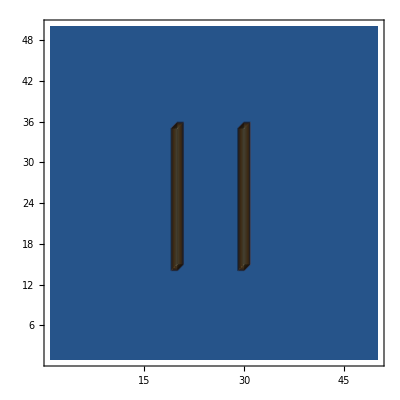

```mathematica
Clear[ϕ]
ϕ = Table[0, 50,50];
Do[
ϕ[[j,20]] = 1;
ϕ[[j,30]] =1 ,
{j,15,35}]

ListContourPlot[ϕ]
```

```mathematica
ListContourPlot[ϕ]
```

-Graphics-

```mathematica
Clear[upd]

upd[ϕ_List]:=
Module[
{ϕp},
ϕp=ϕ;
Do[
ϕp[[i,j]]= 1/4(ϕp[[i+1,j]] + ϕp[[i-1,j]] + ϕp[[i, j+1]]+ ϕp[[i,j-1]]),
{i,2,49},{j,2,49}];
Do[
ϕp[[j,20]] = 1;
ϕp[[j,30]] =1 ,
{j,15,35}];ϕp]
```

```mathematica
ϕ1 =Nest[
upd[#] &, ϕ, 50];
```

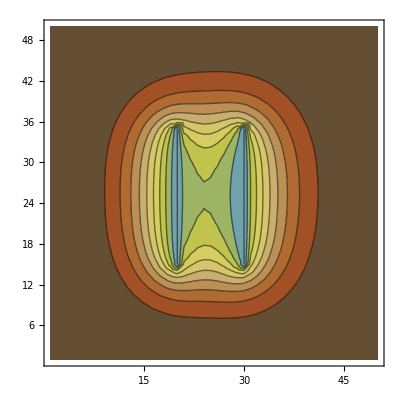

```mathematica
ListContourPlot[ϕ1,Mesh->False,ColorFunction->"SouthwestColors"]
```

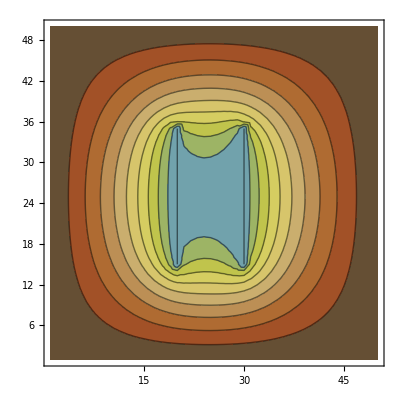

```mathematica
ϕ2 = Nest[upd[#] &, ϕ, 200];

ListContourPlot[ϕ2, Mesh->False, ColorFunction->"SouthwestColors"]
```

more spread out

## Question 11

```mathematica
SeedRandom[2014]
```

```mathematica
t[j_] := j δt

Wj[np_,ns_] := 
Module[
{},
```